## Plot design

### General design

```mathematica
Quiet@Map[SetOptions[#,BaseStyle->{FontSize->18,FontWeight->Plain,FontFamily->"Helvetica",FontColor->Black,Bold},LabelStyle->Black,Frame->True,Axes->None,FrameTicksStyle->Black,FrameTicks->{{Automatic,None},{Automatic,None}},FrameStyle->Thickness[0.0025],Method->{"TransparentPolygonMesh"->True}]&,InputForm[Symbol/@Names["System`*Plot"]]];
```

## Air Density, according to the COSPAR International Reference Atmosphere 1986 model.

```mathematica
Import[NotebookDirectory[]<>"atmosden.gif"] (*Retrieved from the Australian Space Academy: https://www.spaceacademy.net.au/watch/debris/atmosmod.htm*)
```

-Graphics-

```mathematica
polyfn[h_]:=((((((a7*h+a6)*h+a5)*h+a4)*h+a3)*h+a2)*h+a1)*h+a0;
a0:=7.001985 10^-2;
a1:=-4.336216 10^-3;
a2:=-5.009831 10^-3;
a3:=1.621827 10^-4;
a4:=-2.471283 10^-6;
a5:=1.904383 10^-8;
a6:=-7.189421 10^-11;
a7:=1.060067 10^-13;
```

```mathematica
ρ[h_]:=10^polyfn[h] ;  (*kg/m^3*)
```

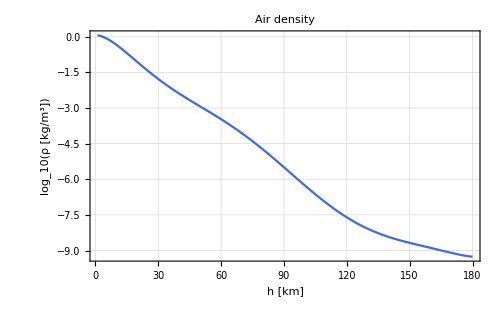

```mathematica
Plot[Log[10,ρ[h]],{h,1,180},PlotStyle->RoyalBlue,FrameLabel->{Style["h [km]",Bold],Style["log_10(ρ [kg/m^3])",Bold]},FrameTicks->{{Automatic,None},{Automatic,None}},PlotLabel->Style["Air density",Bold],ImageSize-> 500,GridLines->Automatic]
```

Conversion Factor to cm^3

```mathematica
Subscript[N, A]:=6.022 10^23 (*mol^-1*)
Subscript[m, N]:=14/Subscript[N, A] 10^-3 (*kg*)
C0:=1 10^-6 1/Subscript[m, N](*m^3/cm^3 × (N atoms)/kg*)
```

```mathematica
ρN[h_]:=C0 ρ[h] (*(N atoms)/cm^3*)
```

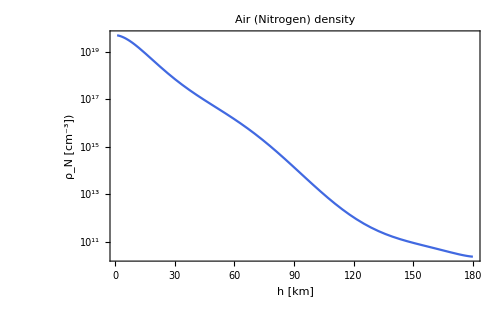

```mathematica
LogPlot[ρN[h],{h,1,180},PlotStyle->RoyalBlue,FrameLabel->{Style["h [km]",Bold],Style["ρ_N [cm^-3])",Bold]},FrameTicks->{{Automatic,None},{Automatic,None}},PlotLabel->Style["Air (Nitrogen) density",Bold],ImageSize-> 500,GridLines->Automatic]
```